```mathematica
toGraphicsList[xs_List] :=( Graphics[{#, EdgeForm[{Thin, Black}], Disk[]}])& /@xs
```

```mathematica
toGraphicsRow[ms_List] :=Join[toGraphicsList[Reverse[ms[[1]]]], {Graphics[{White, EdgeForm[{Thick, Black}], Rectangle[]}]}, toGraphicsList[ms[[2]]]]
```

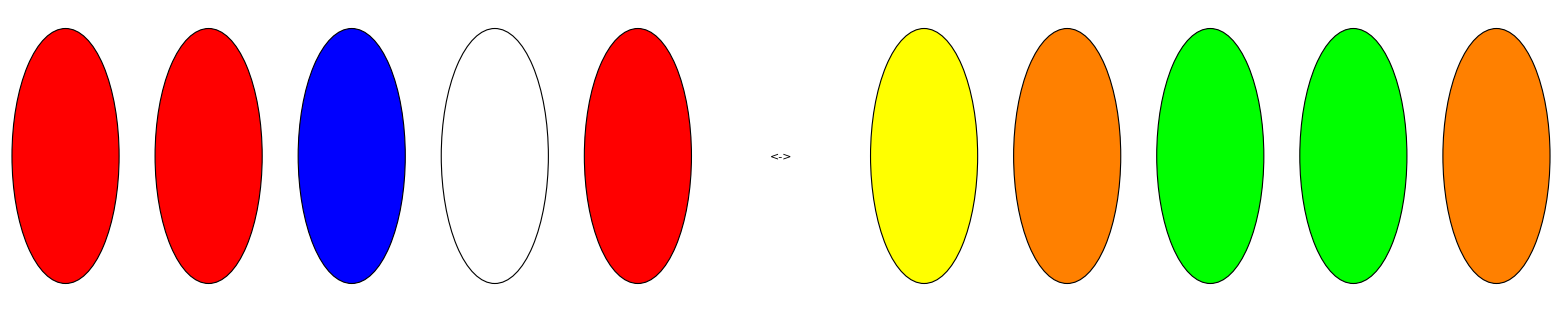

```mathematica
toGraphicsRow[Table[RandomChoice[{Red, White, Blue}], 5], Table[RandomChoice[{Green, Orange, Yellow}], 5]]
```

```mathematica
majority[{{}, ys_List}] := {{}, ys};
```

```mathematica
majority[{xs_List, {}}] := {Drop[xs, 1], {First[xs]}};
```

```mathematica
majority[{xs_List, ys_List}]:= Module[{x, y},
x = First[xs];
y = First[ys];
If[SameQ[x, y], {Drop[xs, 1], Prepend[ys, x]}, {Drop[xs, 1], Drop[ys, 1]}]
];
```

```mathematica
majority[{{Red, Red, Blue}, {}}]
```

{{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},RGBColor[1, 0, 0]}

```mathematica
majorityDone[ms_List] := Length[ms[[1]]] > 0;
```

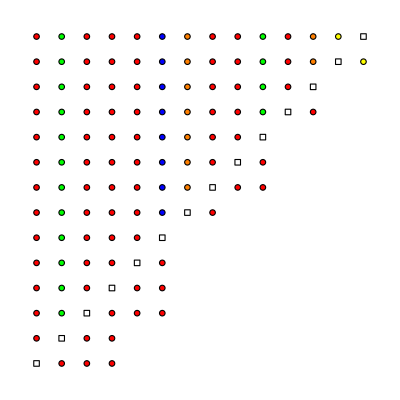

```mathematica
toGraphicsRow[#] & /@  NestWhileList[majority, {{Yellow, Orange, Red, Green, Red, Red, Orange, Blue, Red, Red, Red, Green, Red}, {}}, majorityDone] //GraphicsGrid
```

```mathematica
Show[%65,Background->None]
```

-Graphics-

```mathematica
Show[%68,Background->Directive[RGBColor[0.99,0.,0.02],Opacity[0.]]]
```

-Graphics-

```mathematica
Export["/Users/uwe/Desktop/majority_t6.png",%68,"PNG"]
```

/Users/uwe/Desktop/majority_t6.png

```mathematica
Show[%65,Background->Directive[RGBColor[0.68,0.79,0.97],Opacity[0.]]]
```

-Graphics-

```mathematica
Export["/Users/uwe/Desktop/majority_t7.png",%66,"PNG"]
```

/Users/uwe/Desktop/majority_t7.png

```mathematica
Export["/Users/uwe/Desktop/majority_t5.png",%66,"PNG"]
```

/Users/uwe/Desktop/majority_t5.png